## Solutions: Mathematica 6 Lab 4

Problem 1:

```mathematica
DSolve[y'[x]==-Cos[x]y[x],y[x],x]
```

{{y[x]→ⅇ^(-Sin[x]) C[1]}}

```mathematica
somesolutions=Table[ⅇ^(-Sin[x]) C[1]/.C[1]->i,{i,-5,5}]
```

{-5 ⅇ^(-Sin[x]),-4 ⅇ^(-Sin[x]),-3 ⅇ^(-Sin[x]),-2 ⅇ^(-Sin[x]),-ⅇ^(-Sin[x]),0,ⅇ^(-Sin[x]),2 ⅇ^(-Sin[x]),3 ⅇ^(-Sin[x]),4 ⅇ^(-Sin[x]),5 ⅇ^(-Sin[x])}

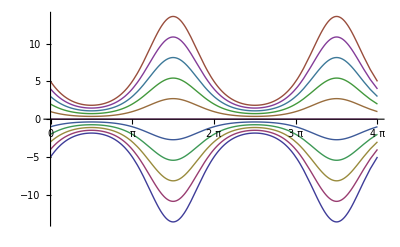

```mathematica
Plot[somesolutions,{x,0,4π},Ticks->{{0,π,2π,3π,4π},Automatic}]
```

Problem 2:

```mathematica
DSolve[x''[t]+(1/3 x'[t]^2-1)x'[t]+x[t]==0,x[t],t]
```

DSolve[x[t]+x'[t] (-1+1/3 x'[t]^2)+x''[t]==0,x[t],t]

```mathematica
violin1=x[t]/.First[NDSolve[{x''[t]+(1/3 x'[t]^2-1)x'[t]+x[t]==0,x[0]==0.1,x'[0]==0},x[t],{t,0,15}]]
violin2=x[t]/.First[NDSolve[{x''[t]+(1/3 x'[t]^2-1)x'[t]+x[t]==0,x[0]==1.0,x'[0]==0},x[t],{t,0,15}]]
violin3=x[t]/.First[NDSolve[{x''[t]+(1/3 x'[t]^2-1)x'[t]+x[t]==0,x[0]==1.9,x'[0]==0},x[t],{t,0,15}]]
```

InterpolatingFunction[{{0.,15.}},<>][t]

InterpolatingFunction[{{0.,15.}},<>][t]

InterpolatingFunction[{{0.,15.}},<>][t]

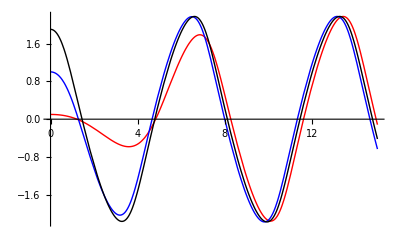

```mathematica
Plot[{violin1,violin2,violin3},{t,0,15},
PlotStyle->{Red,Blue,Black}]
```

Problem 3:

```mathematica
hardspring1=x[t]/.First[NDSolve[{x''[t]+0.3x[t]+0.04 x[t]^3==0,x[0]==0,x'[0]==1},x[t],{t,0,15}]]
hardspring2=x[t]/.First[NDSolve[{x''[t]+0.3x[t]+0.04 x[t]^3==0,x[0]==0,x'[0]==2},x[t],{t,0,15}]]
hardspring3=x[t]/.First[NDSolve[{x''[t]+0.3x[t]+0.04 x[t]^3==0,x[0]==0,x'[0]==3},x[t],{t,0,15}]]
hardspring4=x[t]/.First[NDSolve[{x''[t]+0.3x[t]+0.04 x[t]^3==0,x[0]==0,x'[0]==4},x[t],{t,0,15}]]
hardspring5=x[t]/.First[NDSolve[{x''[t]+0.3x[t]+0.04 x[t]^3==0,x[0]==0,x'[0]==5},x[t],{t,0,15}]]
```

InterpolatingFunction[{{0.,15.}},<>][t]

InterpolatingFunction[{{0.,15.}},<>][t]

InterpolatingFunction[{{0.,15.}},<>][t]

«2 more identical outputs»

```mathematica
colorcod={Blue,Green,Orange,Red,Black}
```

{RGBColor[0,0,1],RGBColor[0,1,0],RGBColor[1,0.5,0],RGBColor[1,0,0],GrayLevel[0]}

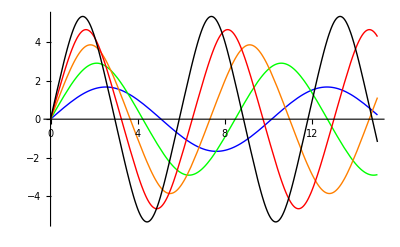

```mathematica
Plot[Evaluate[{hardspring1,hardspring2,hardspring3,hardspring4,hardspring5}],{t,0,15},PlotStyle->colorcode]
```

```mathematica
Clear[x,t,v]
```

```mathematica
hardspring[v_]:=x[t]/.First[NDSolve[{x''[t]+0.3x[t]+0.04 x[t]^3==0,x[0]==0,x'[0]==v},x[t],{t,0,15}]]
```

```mathematica
Manipulate[Plot[Evaluate[hardspring[v]],{t,0,15}, PlotRange->{-6,6}, PlotStyle->{Red,Thick}],{v,1,5}]
```

Problem 4:

```mathematica
tired1=x[t]/.First[DSolve[{x''[t]+4 ⅇ^(-t/4)x[t]==0,x'[0]==0,x[0]==1},x[t],t]]
tired2=x[t]/.First[DSolve[{x''[t]+4 ⅇ^(-t/4)x[t]==0,x'[0]==0,x[0]==2},x[t],t]]
tired3=x[t]/.First[DSolve[{x''[t]+4 ⅇ^(-t/4)x[t]==0,x'[0]==0,x[0]==3},x[t],t]]
tired4=x[t]/.First[DSolve[{x''[t]+4 ⅇ^(-t/4)x[t]==0,x'[0]==0,x[0]==4},x[t],t]]
tired5=x[t]/.First[DSolve[{x''[t]+4 ⅇ^(-t/4)x[t]==0,x'[0]==0,x[0]==5},x[t],t]]
```

(BesselJ[1,16] BesselY[0,16 √(ⅇ^(-t/4))]-BesselJ[0,16 √(ⅇ^(-t/4))] BesselY[1,16])/(BesselJ[1,16] BesselY[0,16]-BesselJ[0,16] BesselY[1,16])

(2 (BesselJ[1,16] BesselY[0,16 √(ⅇ^(-t/4))]-BesselJ[0,16 √(ⅇ^(-t/4))] BesselY[1,16]))/(BesselJ[1,16] BesselY[0,16]-BesselJ[0,16] BesselY[1,16])

(3 (BesselJ[1,16] BesselY[0,16 √(ⅇ^(-t/4))]-BesselJ[0,16 √(ⅇ^(-t/4))] BesselY[1,16]))/(BesselJ[1,16] BesselY[0,16]-BesselJ[0,16] BesselY[1,16])

(4 (BesselJ[1,16] BesselY[0,16 √(ⅇ^(-t/4))]-BesselJ[0,16 √(ⅇ^(-t/4))] BesselY[1,16]))/(BesselJ[1,16] BesselY[0,16]-BesselJ[0,16] BesselY[1,16])

(5 (BesselJ[1,16] BesselY[0,16 √(ⅇ^(-t/4))]-BesselJ[0,16 √(ⅇ^(-t/4))] BesselY[1,16]))/(BesselJ[1,16] BesselY[0,16]-BesselJ[0,16] BesselY[1,16])

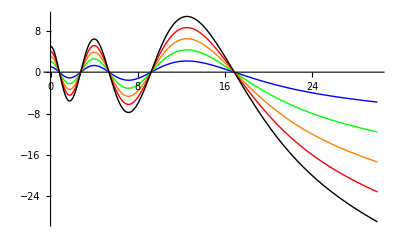

```mathematica
Plot[Evaluate[{tired1,tired2,tired3,tired4,tired5}],{t,0,30},PlotStyle->colorcode]
```

Problem 5:

```mathematica
DSolve[x''[t]+(1+0.2Sin[2t])x[t]==0,x[t], t]
```

DSolve[(1+0.2 Sin[2 t]) x[t]+x''[t]==0,x[t],t]

```mathematica
stimulated=x[t]/.NDSolve[{x''[t]+(1+.2Sin[2t])x[t]==0,
x'[0]==0,x[0]==1},x[t],{t,0,50}]
unstimulated=x[t]/.NDSolve[{x''[t]+(1+0.0Sin[2t])x[t]==0,
x'[0]==0,x[0]==1},x[t],{t,0,50}]
```

{InterpolatingFunction[{{0.,50.}},<>][t]}

{InterpolatingFunction[{{0.,50.}},<>][t]}

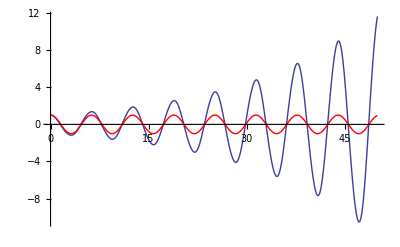

```mathematica
Plot[{stimulated,unstimulated},{t,0,50},PlotRange->All,PlotStyle->{{},Red}]
```

```mathematica
outofsync=x[t]/.NDSolve[{x''[t]+(1+0.2Sin[2.2t])x[t]==0,
x'[0]==0,x[0]==1},x[t],{t,0,50}]
```

{InterpolatingFunction[{{0.,50.}},<>][t]}

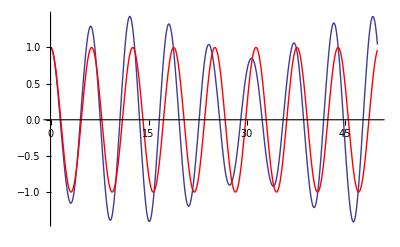

```mathematica
Plot[{outofsync,unstimulated},{t,0,50},
PlotStyle->{{},Red}]
```